```mathematica
Needs["WLGPNTeam`TimeDepthModels`"]
```

```mathematica
listH ={100,100,100, 100}
alpha = 0 Degree
len = 100
dx = 10
anoMaxDisp = 0
hTapering = 1
listV = {100,100,100,100, 100}
```

{100,100,100,100}

0

100

10

0

1

{100,100,100,100,100}

```mathematica
horNHsorted = BuildDepthSection[listH,alpha,len,dx,anoMaxDisp,hTapering][["horNHsorted"]]
```

{{{10,-1},{20,1},{30,1},{40,-3},{50,-8},{60,-12},{70,-13},{80,-13},{90,-10},{100,-7}},{{10,-100},{20,-100},{30,-100},{40,-100},{50,-100},{60,-100},{70,-100},{80,-100},{90,-100},{100,-100}},{{10,-200},{20,-200},{30,-200},{40,-200},{50,-200},{60,-200},{70,-200},{80,-200},{90,-200},{100,-200}},{{10,-300},{20,-300},{30,-300},{40,-300},{50,-300},{60,-300},{70,-300},{80,-300},{90,-300},{100,-300}},{{10,-400},{20,-400},{30,-400},{40,-400},{50,-400},{60,-400},{70,-400},{80,-400},{90,-400},{100,-400}}}

```mathematica
PlotDepthSection[horNHsorted]
```

-Graphics-

```mathematica
velModel=BuildVelocitySection[horNHsorted,listV][["velModel"]]
```

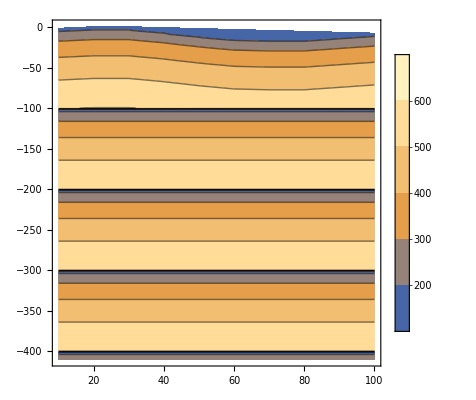

```mathematica
PlotVelocity[velModel]
```

```mathematica
timeNH=BuildTimeSection[horNHsorted, velModel][["timeNH"]]
```

{{{10,-0.0046435},{20,0.00460777},{30,0.00460777},{40,-0.0140404},{50,-0.0382097},{60,-0.0582969},{70,-0.0634305},{80,-0.0634305},{90,-0.048166},{100,-0.0332954}},{{10,-0.468078},{20,-0.457041},{30,-0.457041},{40,-0.479182},{50,-0.507226},{60,-0.52994},{70,-0.535652},{80,-0.535652},{90,-0.518556},{100,-0.501587}},{{10,-1.39406},{20,-1.38124},{30,-1.38124},{40,-1.40689},{50,-1.43897},{60,-1.4646},{70,-1.471},{80,-1.471},{90,-1.45179},{100,-1.43256}},{{10,-2.7826},{20,-2.76799},{30,-2.76799},{40,-2.79716},{50,-2.8333},{60,-2.86191},{70,-2.86901},{80,-2.86901},{90,-2.84765},{100,-2.8261}},{{10,-4.70105},{20,-4.6824},{30,-4.6824},{40,-4.7196},{50,-4.76546},{60,-4.80157},{70,-4.8105},{80,-4.8105},{90,-4.7836},{100,-4.75635}}}

```mathematica
PlotTimeSection[timeNH]
```

-Graphics-